## Parameterized Curves Assignment

### Instructions

The purpose of this assignment is to assess your ability to define and work with parametric equations. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

Due Date:
see Canvas

### Question 1: Tangent Lines of Parametric Functions

If a projectile is fired with an initial velocity of v_0 meters per second at an angle α above the horizontal and we assume air resistance is negligible, then its position after t seconds is given by the parametric equations 
x=t (v_0 cos α) 
y=t (v_0 sin α)-1/2 g t^2
where g is the acceleration due to gravity, 9.8 m/s^2.

Suppose a gun is fired with α = π/4 and v_0 = 400 m/s.

a) At the point where the bullet achieves its maximum height, the slope of the line tangent to the trajectory curve is 0.  Use this information to determine the time the bullet achieves maximum height.

```mathematica
g=9.8;
α=π/4;
Subscript[v, 0]=400;
x[t_]:=t Subscript[v, 0] Cos[α];
y[t_]:=t Subscript[v, 0] Sin[α]-1/2 g t^2;
FindRoot[y'[t]/x'[t]==0,{t,20}]
```

{t→28.8615}

b) Find the slope of the tangent line when the time is about 12 seconds.

```mathematica
slope =y'[12]/x'[12]
```

0.584221

c) What is the maximum height achieved by the bullet?

```mathematica
y[t]/.FindRoot[y'[t]/x'[t]==0,{t,20}]
```

4081.63

```mathematica
4081.632653061225m
```

4081.63 m

### Question 2: Arc Length

a) Plot the epitrochoid with equations
x=13cos t -2.5 cos (13t)/2 
y=13sin t -2.5 sin (13t)/2
Use a range of t=0 to t=4π.

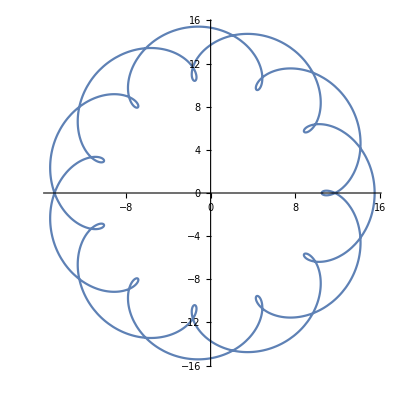

```mathematica
x[t_]:=13Cos[t]-2.5Cos[(13t)/2];
y[t_]:=13Sin[t]-2.5Sin[(13t)/2];
ParametricPlot[{x[t],y[t]},{t,0,4π}]
```

b) Use the NIntegrate command to find the approximate length of the curve you just plotted.  You may want to check your integral setup by first computing the arc length of a circle using a parameterized representation.

```mathematica
NIntegrate[√((x'[t])^2+(y'[t])^2),{t,0,4π}]
```

238.471

### Question 3: Surface Area

a) Define and plot a parametric curve that starts at the point (0,2) (i.e. is at (0,2) when t=0) and travels along the curve defined by x=t, y=(ⅇ^t+13)/7.  Use a range of t=0 to t=4 for your plot.

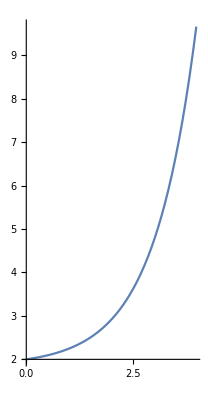

```mathematica
x[t_]:=t;
y[t_]:=(ⅇ^t+13)/7;
ParametricPlot[{x[t],y[t]},{t,0,4}]
```

b) Find the arc length of the parametric function from t=0 to t=4.

```mathematica
NIntegrate[√((x'[t])^2+(y'[t])^2),{t,0,4}]
```

9.36969

c) Use the NIntegrate command and the equations you defined in Part a to find the area of the surface that results from rotating your curve about the y-axis.

```mathematica
NIntegrate[2π x[t] √((x'[t])^2+(y'[t])^2),{t,0,4}]
```

161.775

d) Use the NIntegrate command and the equations you defined in Part a to find the area of the surface that results from rotating your curve about the x-axis.

```mathematica
NIntegrate[2π y[t] √((x'[t])^2+(y'[t])^2),{t,0,4}]
```

309.762

e) Use the RevolutionPlot3D command and the equations you defined in Part a to plot surface that results from rotating your curve about the x-axis.  Remember to use the Rasterize command on this 3D plot before you save to a pdf.

```mathematica
Rasterize[RevolutionPlot3D[{x[t],y[t]},{t,0,4 },RevolutionAxis->{1, 0, 0},Axes-> True,Boxed->False,AxesOrigin->{0,0,0}]]
```

-Graphics-